```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/SMS-stop_SMQCD/SMS-stop_SMQCD",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

FR$ClassesTranslation

## Top Self Energy

### Remove diagrams which are identically zero due to color conservation

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 1 Particles insertion

in total: 1 Particles amplitude

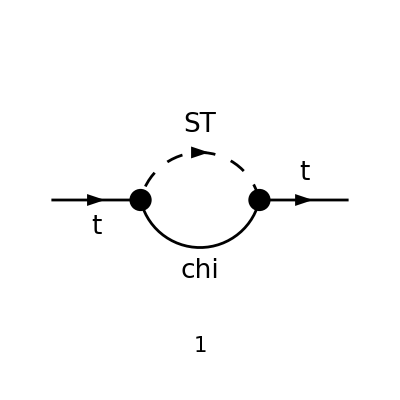

```mathematica
tops = CreateTopologies[1, 1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processTT =  { F[3]} -> {F[3]};
allDiags = InsertFields[tops,processTT, InsertionLevel-> {Particles},ExcludeParticles->{V[1]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->True,TransversePolarizationVectors->{p1,p2},DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

-((-ⅈ yDM (γ̄)^7 δ_Col1Col2).(mChi+γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-mChi^2).((q-p)^2-mST^2))

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

(yDM^2 δ_Col1Col2 (γ·q).(γ̄)^6)/((q^2-mChi^2).((p-q)^2-mST^2))

```mathematica
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

-ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 B_1(p^2,mChi^2,mST^2)

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampC]]
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(2 ε_UV)

```mathematica
ampCeval=PaXEvaluate[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]
```

-(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 (log(mChi^2/mST^2)-2 log(μ^2/mST^2)+2 ℽ-4-2 log(4 π)+4 log(π)+4 log(1/(2 π))+log(16)))/(64 π^2)+(ⅈ yDM^2 δ_Col1Col2 √(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4) (γ·p).(γ̄)^6 log((√(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4)+mChi^2+mST^2-p^2)/(2 mChi mST)))/(32 π^2 p^2)+(ⅈ yDM^2 (mChi-mST) (mChi+mST) δ_Col1Col2 √(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4) (γ·p).(γ̄)^6 log((√(-2 p^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p^4)+mChi^2+mST^2-p^2)/(2 mChi mST)))/(32 π^2 p^4)+(ⅈ yDM^2 δ_Col1Col2 (mST^2 log(mChi^2/mST^2)+mChi^2-mST^2) (γ·p).(γ̄)^6)/(32 π^2 p^2)-(ⅈ yDM^2 (mChi-mST)^2 (mChi+mST)^2 δ_Col1Col2 log(mChi^2/mST^2) (γ·p).(γ̄)^6)/(64 π^2 p^4)+(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)

```mathematica
FCClearScalarProducts[];
ScalarProduct[p,p]=MT^2;
```

```mathematica
ampCsimp=FullSimplify[SUNSimplify[FCTraceFactor[ampCeval]],Assumptions->{mST>0,mChi>0,MT>0}]
```

-1/(32 π^2 ε MT^4)ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 (ε MT^2 (mST^2-mChi^2)+ε (-2 mChi^2 mST^2+mChi^4+(mST^2-MT^2)^2) log(mChi/mST)+ε √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (mChi^2-mST^2+MT^2) (log(2 mChi mST)-log(mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2))-ε MT^4 log((4 π μ^2)/mST^2)+((ℽ-2) ε-1) MT^4)

```mathematica
Collect[Limit[ampCsimp,mChi->mST],Epsilon]
```

(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)-(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 (MT^4 (-log((4 π μ^2)/mST^2))+MT^2 √(MT^2 (-(2 mST-MT)) (2 mST+MT)) (log(2 mST^2)-log(2 mST^2+√(MT^2 (-(2 mST-MT)) (2 mST+MT))-MT^2))+(ℽ-2) MT^4))/(32 π^2 MT^4)

```mathematica
Collect[Limit[%,MT->0],Epsilon]
```

(ⅈ yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6)/(32 π^2 ε)-(ⅈ yDM^2 δ_Col1Col2 (ℽ-log((4 π μ^2)/mST^2)) (γ·p).(γ̄)^6)/(32 π^2)